# Lista III - Física Matemática 1

Lyliana Myllena Santos de Sousa - 11223740
Lyliana.Sousa@usp.br

## 1.a)

Dada a equação de calor em uma dimensão, com as condições de Dirichlet a seguir: 𝓊_t=𝓊_xx (1.1), 𝓊(0,t)=𝓊(1,t)=0 (1.2),  t>0, 𝓊(x,0)=x(1-x) (1.3), x∈[0,1] (1.4). Para descobrirmos a solução de 𝓊, usaremos o método da separação de variáveis, onde 𝓊 terá o seguinte formato: 𝓊(x,t)=X(x)T(t) (1.5), usaremos esse formato de 𝓊 na Eq.(1.1), que multiplicaremos o lado direito por α para que possamos utilizar as soluções nas próximas questões. Assim, teremos: 
→  𝓊_t=𝓊_xx → X  Ṫ = α T X''→ (Ṫ)/αT=X''/X= -k.b2, onde k é uma constante. Disso tiramos o seguinte sistema: Piecewise[{{Ṫ = -αk.b2T, }, {X''=-k.b2X, }}](1.6), que a solução consiste  na solução das EDOs. Piecewise[{{T(t)= ℯ^(-αk.b2t), }, {X(x) = aCos(kx) + bSin(kx), }}](1.7). Assim, a nossa solução terá o seguinte formato, para α = 1:  𝓊(x,t)=ℯ^(-k.b2t) [aCos(kx) + bSin(kx)] (1.8). Aplicando as condições de contorno, temos:
→  𝓊(0,t)=ℯ^(-k.b2t) [aCos(kx) + bSin(kx)]=0 → a = 0 (1.9)
→ 𝓊(1,t)=ℯ^(-k.b2t)  bSin(kx)=0 → k = nπ (1.10), para n = 1, 2, 3 ...
Portanto, das condições de contorno, tiramos que por linearidade :  𝓊(x,t)=∑_(n=1)^∞ b_n ℯ^(-k_n^2t) Sin(kx) (1.11), onde b_n dependerá das condições iniciais.
Tenho que b_n será dado por: b_n= 2/L∫_0^L 𝓊_0 sin(k_n x)ⅆx(1.12), onde L = 1.  Portanto, b_n= 2∫_0^1 x(1-x)sin(k_n x)ⅆx= 2∫_0^1 [ xsin(k_n x) - x.b2sin(k_n x)]ⅆx. Resolvendo as integrais tenho:

```mathematica
2*Integrate[x*Sin[n π x]-x^2*Sin[n π x],{x,0,1}](*1.13*)
```

(2 (2-2 Cos[n π]-n π Sin[n π]))/(n^3 π^3)

```mathematica
FullSimplify[%, n ∈ Integers](*1.14*)
```

-(4 (-1+(-1)^n))/(n^3 π^3)

Assim, b_n=-(4 (-1+(-1)^n))/(n^3 π^3)  (1.15)
Concluímos então que a solução é: 𝓊(x,t)= ∑_(n=1)^∞ -(4 (-1+(-1)^n))/(n^3 π^3)sin(nℼx)ℯ^(-(nℼ).b2t)  (1.16)

```mathematica
nmax1 = 100;
bn1 =-(4 (-1+(-1)^n))/(n^3 π^3);
sol1 = Sum[bn1*Exp[-(n π)^2 t]* Sin[n π*x],{n,1,nmax1}];
```

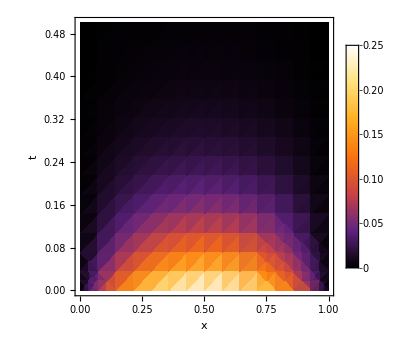

```mathematica
plot1 = DensityPlot[sol1, {x,0,1},{t,0,0.5},
ImageSize->350,
FrameLabel->{"x","t"},
ColorFunction->"SunsetColors",
PlotLegends->Automatic,
PlotRangePadding->None,
PlotRange->All,
LabelStyle->{FontFamily->"Times",20,Black}
]
```

## 1.b)

Dada a equação de calor em uma dimensão, com as condições de Neumann a seguir: 𝓊_t=3 𝓊_xx(1.17), 𝓊_x(0,t)=𝓊_x(1,t)=0 (1.18),  t>0, 𝓊(x,0)=x.b2(3/2-x) (1.19), x∈[0,1].Para esse item, partiremos já da solução da Eq. com α = 3. Com isso, temos:  𝓊(x,t)=ℯ^(-3k.b2t) [aCos(kx) + bSin(kx)] (1.20). As condições de contorno, nos diz que: 𝓊_x(0,t)=𝓊_x(1,t)=0. Disso tiramos: 𝓊_x(x,t)=ℯ^(-3k.b2t) [bk_n Cos(kx) -ak_n Sin(kx)] (1.21)
→ 𝓊_x(0,t)=ℯ^(-3k.b2t) bk =0  →  b = 0 (1.22). 
Já considerando que b = 0, tenho:
→𝓊_x(1,t)=-ℯ^(-3k.b2t) akSin(k)=0 →  k = nπ (1.23), para n = 0, 1, 2, 3 ...
Das condições de contorno tiramos que: 𝓊(x,t)=∑_(n=0)^∞ a_n ℯ^(-3 k_n^2 t)cos(k_n x) = a_0/2 + ∑_(n=1)^∞ a_n ℯ^(-3 k_n^2 t)cos(k_n x) (1.24)
Agora, analisando as condições iniciais, tenho que, sendo 𝓊_0=𝓊(x,0)=x.b2(3/2-x). Vimos em aula que, a_n é dado por: a_n= 2/L∫_0^L 𝓊_0 cos(k_n x)ⅆx (1.25), onde L = 1. Assim, tenho: a_n= 2∫_0^1 𝓊_0 cos(k_n x)ⅆx = 
 2∫_0^1 x.b2(3/2-x)cos(k_n x)ⅆx =  2[3/2∫_0^1 x.b2cos(k_n x)ⅆx - ∫_0^1 x.b3cos(k_n x)ⅆx]

```mathematica
2*Integrate[3/2 x^2*Cos[n π x]-x^3*Cos[n π x],{x,0,1}]
```

(-12+12 Cos[n π]+n π (6+n^2 π^2) Sin[n π])/(n^4 π^4)

```mathematica
FullSimplify[%, n ∈ Integers](*(1.26)*)
```

(12 (-1+(-1)^n))/(n^4 π^4)

Assim, temos:  a_n=(12 (-1+(-1)^n))/(n^4 π^4)(1.26)
Obtenho o a_0 da seguinte forma: a_0= 2/L∫_0^L u_0 ⅆx =   2∫_0^1 u_0 ⅆx =  2∫_0^1 (3/2 x.b2 -x.b3)ⅆx = (2[(x.b3)/2 - x^4/4])_0^1 = 2[1/2-1/4] = 2/4(1.27)
Portanto, a solução será: 𝓊(x,t)=1/4 + ∑_(n=1)^∞ (12 (-1+(-1)^n))/(n^4 π^4)ℯ^(-3 k_n^2 t)cos(k_n x) (1.28)

```mathematica
nmax2 = 100;
an2 = (12 (-1+(-1)^n))/(n^4 π^4);
sol2 = Sum[an2*Exp[-3*(n π)^2 t]* Cos[n π*x],{n,1,nmax2}];
```

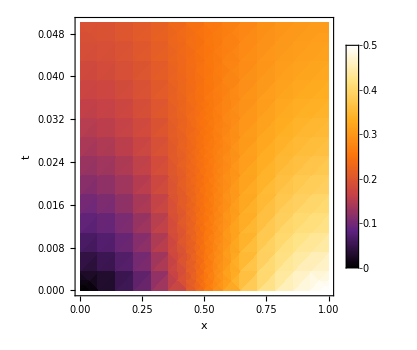

```mathematica
plot = DensityPlot[1/4 + sol2, {x,0,1},{t,0,0.05},
ImageSize->350,
FrameLabel->{"x","t"},
ColorFunction->"SunsetColors",
PlotLegends->Automatic,
PlotRangePadding->None,
PlotRange->All,
LabelStyle->{FontFamily->"Times",20,Black}
]
```

## 1.c)

Resolveremos a equação de calor em uma dimensão para condições Mistas a seguir: 𝓊_t=𝓊_xx (1.29), 𝓊(0,t)=𝓊_x(1,t)=0 (1.30),  t>0, 𝓊(x,0)=x.b2(3/2-x) (1.31), x∈[0,1]. Partindo da Eq. (1.7) , temos a seguinte solução: 𝓊(x,t)=ℯ^(-k.b2t) [aCos(kx) + bSin(kx)] (1.32).
Devido as condições de contorno, temos que:
→ 𝓊(0,t) = ℯ^(-k.b2t)a=0 → a = 0 (1.33)
Assim, tenho que 𝓊(x,t)=ℯ^(-k.b2t) bSin(kx) e  𝓊_x(x,t)=ℯ^(-k.b2t) bkcos(kx) (1.34). Disso, tenho que pela condição de contorno, 𝓊_x(1,t)=ℯ^(-k.b2t) bkcos(k) = 0  → k_n = (1/2 + n)ℼ(1.35), para n = 0, 1, 2 ...
Disso tiramos que: 𝓊(x,t)=∑_(n=0)^∞ b_n ℯ^(-k_n^2t)sin(k_n x)  (1.36). 
Obterei o b_n das condições iniciais: b_n = 2/L∫_0^L 𝓊(x,0)sin(k_n x)ⅆx = 2∫_0^1 [3/2 x.b2sin(k_n x)-x.b3sin(k_n x)]ⅆx

```mathematica
2*Integrate[3/2*x^2*Sin[(1/2+n)  π x]-x^3*Sin[(1/2+n) π x],{x,0,1}]
```

(2 (96 Cos[n π]+(1+2 n) π (-24+(24+(π+2 n π)^2) Sin[n π])))/(π+2 n π)^4

```mathematica
FullSimplify[%, n ∈ Integers]
```

-(48 (-4 (-1)^n+π+2 n π))/(π+2 n π)^4

Disso, tiro que,  b_n=-(48 (-4 (-1)^n+π+2 n π))/(π+2 n π)^4(1.37)
Portanto, nossa solução é: 𝓊(x,t) =∑_(n=0)^∞ -(48 (-4 (-1)^n+π+2 n π))/(π+2 n π)^4 ℯ^(-k.b2t)sin(kx) (1.38)

```mathematica
nmax3 = 100;
k3 = (1/2+n)π;
bn3 = -(48 (-4 (-1)^n+π+2 n π))/(π+2 n π)^4 ;
sol3 = Sum[bn3*Exp[-1*(k3)^2 t]* Sin[k3*x],{n,0,nmax3}];
```

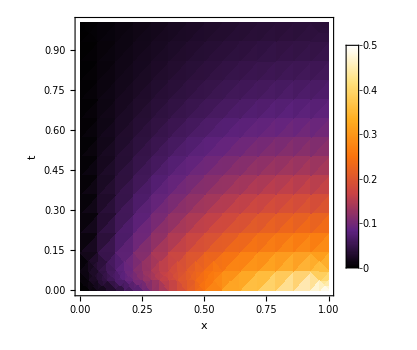

```mathematica
plot = DensityPlot[ sol3, {x,0,1},{t,0,1},
ImageSize->350,
FrameLabel->{"x","t"},
ColorFunction->"SunsetColors",
PlotLegends->Automatic,
PlotRangePadding->None,
PlotRange->All,
LabelStyle->{FontFamily->"Times",20,Black}
]
```

## 2.

A equação de calor em uma dimensão numa barra de -L/2 à L/2 com as condições de contorno de Dirichlet.  Com isso, temos que: 𝓊_t= α 𝓊_xx (2.1), com 𝓊(-L/2,t) = 𝓊(L/2,t) = 0 (2.2) e 𝓊_0(x) (2.3). Dessa vez, usarei a solução do espaço como sendo: X(x) = Asin(kx + ϕ)(2.4). Assim a solução geral é: 𝓊(x,t)=ℯ^(-αk.b2t) Asin(kx+ϕ) (2.5)
Com isso, aplicando as condições de contorno, tenho: 
→ 𝓊(-L/2,t)=ℯ^(-k.b2t) Asin(-kL/2+ϕ)=0 → -kL/2+ϕ = nℼ
→ 𝓊(L/2,t)=ℯ^(-k.b2t) Asin(kL/2+ϕ)=0 → kL/2+ϕ = nℼ
Nosso k deve ser diferente de zero, com isso temos:  k = nℼ/L (2.6) e o ϕ será dado em função de k, assim o ϕ =nℼ/2=kL/2 (2.7)
Disso temos a solução: 𝓊(x,t)=∑_(n=1)^∞ a_n ℯ^(-αk.b2t) sin(nℼ/L[x+L/2]) (2.8).
Obtemos a_npela condição inicial: a_n=2/L∫_(-L/2)^(L/2) 𝓊_0 cos(nℼ/L[x+L/2])ⅆx (2.8).
Com isso, nossa solução é: 𝓊(x,t)=∑_(n=1)^∞ 2/L∫_(-L/2)^(L/2) 𝓊_0 cos(nℼ/L[x+L/2])ⅆx ℯ^(-αk.b2t) sin(nℼ/L[x+L/2]) (2.10)

## 3.a)

Oscilador harmonico quântico é descrita por uma Hamitoniana: H= (p.b2)/(2m)+1/2 mω.b2x.b2(3.1), onde H é um operador diferencial em x e sendo p=-ⅈℏ ⅆ/ⅆx (3.2). Considerando os operadores diferenciais, a=√(mω/(2ℏ))(x + ⅈp/mω) (3.3) e  a^†=√(mω/(2ℏ))(x - ⅈp/mω)(3.4).  Analisaremos agora o comutador de a_e a^†, lembrando que [a,b]= ab-ba (3.5) e que [x,p] = ⅈℏ =xp-px (3.6)
→ [ a_, a^†] = mω/(2ℏ)[x+ⅈp/mω, x-ⅈp/mω]= mω/(2ℏ)[(x+ⅈp/mω)( x-ⅈp/mω)  - (x-ⅈp/mω)( x+ⅈp/mω)]
=mω/(2ℏ)[x.b2-ⅈxp/mω+ ⅈpx/mω+(p/mω).b2  - x.b2-ⅈxp/mω +ⅈpx/mω-(p/mω).b2] = ⅈ/(2ℏ)(-xp+px-xp+px) = ⅈ/(2ℏ)(-2ⅈℏ) = 1 (3.7)

## 3.b)

Agora mostrarei que a Hamiltoniana pode ser escrita como H= ℏω(a^†a + 1/2) (3.8). 
→ a^†a = √(mω/(2ℏ))(x - ⅈp/mω)√(mω/(2ℏ))(x + ⅈp/mω) = mω/(2ℏ)(x.b2 + ⅈxp/mω - ⅈpx/mω + (p.b2)/(m.b2ω.b2)) = mω/(2ℏ)(x.b2  - ℏ/mω + (p.b2)/(m.b2ω.b2)) = (mωx.b2)/(2ℏ)  + (p.b2)/(2ℏmω) -1/2
→ a^†a + 1/2= (mωx.b2)/(2ℏ)  + (p.b2)/(2ℏmω)
→ ℏω(a^†a + 1/2) = (mω.b2x.b2)/2+(p.b2)/(2m)=H (3.9)

## 3.c)

Considerando a ψ(x)=0 (3.10), que é uma equação ordinária diferencial, encontrarei a solução. 
→ a ψ_0(x)=0 → √(mω/(2ℏ))(x + ⅈp/mω)ψ_0(x)=0 →(x + ⅈp/mω)ψ_0(x)=0 → x ψ_0(x)+ ℏ/mω ⅆ/ⅆx ψ_0(x)=0 → x ψ_0(x)=- ℏ/mω(ⅆψ_0(x))/ⅆx → -mω/ℏx ⅆx=(ⅆψ_0(x))/(ψ_0(x)) → ln|ψ_0(x)|= -mω/(2ℏ)x.b2 + constante →  ψ_0(x)=α ℯ^(-mω/(2ℏ)x.b2) (3.11). Devo escolher uma valor de α para que a função seja normalizada: ∫_(-∞)^∞ |ψ_0(x)|.b2ⅆx = ∫_(-∞)^∞ α.b2 ℯ^(-mω/ℏx.b2)ⅆx= (√ℼ α.b2)/(√(mω/ℏ))=1 (3.12), com isso, tenho: α = (mω/ℼℏ)^(1/4) (3.13). Com isso temos que, ψ_0(x)= (mω/ℼℏ)^(1/4) ℯ^(-mω/(2ℏ)x.b2) (3.14)

## 4.

Encontraremos a solução da equação de onda em uma dimensão, com as seguintes condições: 𝓊_tt= 𝓊_xx (4.1), 𝓊(0,t) = 𝓊(1,t) = 0 (4.2), 𝓊(x,0) = x(1-x) (4.3), 𝓊_t(x,0)=0 (4.4), t>0 ,  x ∈ [0,1]. Usaremos os mesmos princípios anteriores, onde 𝓊(x,t)=X(x)T(t) (4.5). Disso temos que, 𝓊_tt= 𝓊_xx <-> X T^(..) = TX'' ⇒ T^(..)/T=X''/X=-k.b2 (4.6). Disso obtemos o sistema:  Piecewise[{{T^(..) = -αk.b2T, }, {X''=-k.b2X, }}](4.7). Disso eu tiro as seguintes soluções: X(x)=Acos(kx)+Bsen(kx) (4.8) e T(t)= Ã ℯ^ⅈkt+B̃ ℯ^-ⅈkt  (4.9). Logo, nossa a solução geral é: 𝓊(x,t)= [Acos(kx)+Bsen(kx)][ Ã ℯ^ⅈkt+B̃ ℯ^-ⅈkt] (4.10). Usando as condições de contorno, temos que:
→ 𝓊(0,t)= A[ Ã ℯ^ⅈkt+B̃ ℯ^-ⅈkt] = 0 →  A = 0 (4.11)
→  𝓊(1,t)= Bsen(k)[ Ã ℯ^ⅈkt+B̃ ℯ^-ⅈkt] = 0 → k = nℼ (4.12), para n = 1, 2, 3...
→ 𝓊_t(x,t)= [Acos(kx)+Bsen(kx)][ Ãⅈk ℯ^ⅈkt-B̃ ⅈkℯ^-ⅈkt] 
    𝓊_t(x,0)= [Acos(kx)+Bsen(kx)][ Ãⅈk-B̃ ⅈk ] = 0 →  Ã = B̃ (4.13).
Juntando todas as constantes em uma só, tenho que: 𝓊(x,t)=∑_(n=1)^∞ b_n sen(nℼx)[  ℯ^ⅈkt+ℯ^-ⅈkt] (4.14), onde o b_n é dado pela condição inicial: b_n=2/L∫_0^L 2x(1-x)sen(nℼx)ⅆx = 4∫_0^1 x(1-x)sen(nℼx)ⅆx =  4∫_0^1 [xsen(nℼx)-x.b2sen(nℼx)]ⅆx.
Podemos observar que esse é o mesmo b_n de item 1.a), só que dividida por 2. Logo, nosso b_né  b_n=-(4 (-1+(-1)^n))/(2*n^3 π^3) (4.15). Assim, nossa solução é:
𝓊(x,t)=∑_(n=1)^∞ -(4 (-1+(-1)^n))/(2*n^3 π^3)sen(nℼx)[  ℯ^ⅈkt+ℯ^-ⅈkt] (4.16)
Um resultado muito parecido com o item 1.a), eles são diferentes apenas pelo fator 2 e pelas exponenciais.

```mathematica
nmax4 = 100;
k4 = n*π;
bn4 = -(4 (-1+(-1)^n))/(2*n^3 π^3) ;
sol4 = Sum[bn4* Sin[k4*x]*(Exp[ⅈ*k4* t]+Exp[-ⅈ*k4* t]),{n,1,nmax4}];
```

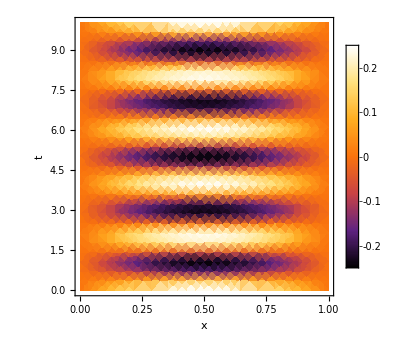

```mathematica
plot = DensityPlot[ sol4, {x,0,1},{t,0,10},
ImageSize->350,
FrameLabel->{"x","t"},
ColorFunction->"SunsetColors",
PlotLegends->Automatic,
PlotRangePadding->None,
PlotRange->All,
LabelStyle->{FontFamily->"Times",20,Black}
]
```

## 5.a)

Encontrando a solução geral para a equação de Klein-Gordon 𝓊_tt=(c.b2𝓊)_xx-μ.b2𝓊 (5.1), 𝓊(0,t)=𝓊(L,t)=0 (5.2), 𝓊(x,0)=𝒻(x) (5.3), 𝓊_t(x,0)=ℊ(x) (5.4), onde μ é uma constante. Basicamente, isso é uma equação de onda com uma força restauradora de -μ.b2𝓊.
Para isso, assumo que a nossa solução será do formato 𝓊(x,t)=X(x)T(t) (5.5), assim, 𝓊_xx=X T^(..) (5.6) e 𝓊_tt=TX'' (5.7). 
→ 𝓊_tt=(c.b2𝓊)_xx-μ.b2𝓊 → TX''=c.b2 X T^(..)-μ.b2XT. Isolando a parte temporal da espacial, temos:
→ T^(..)/(c.b2T) + (μ.b2)/(c.b2) = X''/X=-k.b2. Disso, tenho o sistema  de EDOs Piecewise[{{T^(..)=-(k.b2c.b2 +μ.b2)T, T(t)= ã cos(Et)+ b̃ sen(Et)}, {X''=-k.b2X, X(x)=acos(kx)+bsen(kx)}}] (5.8), onde chamo E=k.b2c.b2 +μ.b2.
Assim, nossa solução geral é: 𝓊(x,t)=[ ã cos(Et)+ b̃ sen(Et)][acos(kx)+bsen(kx)] (5.9).
Das condições de contorno, tiro:
→ 𝓊(0,t)=T a=0  ⇒ a =0 (5.10)
Já utilizando que a = 0, tenho
→ 𝓊(L,t)=T b sen (kL) = 0 ⇒ k_n=nπ/L (5.11), para n = 1, 2, 3 ...
A partir das condições de contorno e incorporando a constante b nas constantes ã e  b̃, nossa solução fica: 𝓊(x,t)=∑_(n=1)^∞ [OverTilde[a_n]cos(E_n t)+ (b̃)_n sen(E_n t)]sen(k_n x) (5.12). 
Agora analisarei as condições iniciais. Assim,
→ 𝓊(x,0)=∑_(n=1)^∞ OverTilde[a_n]sen(k_n x)=𝒻(x). Logo, pelo que vimos nas notas de aula OverTilde[a_n]=2/L∫_0^L 𝒻(x)sen(k_n x)ⅆx (5.13)
Agora, sendo 𝓊_t(x,t)=∑_(n=1)^∞ [-(ã)_n E_n sen(Et)+ (b̃)_n E_n cos(E_n t)]sen(k_n x), temos que 
→ 𝓊_t(x,0)=∑_(n=1)^∞ (b̃)_n E_n sen(k_n x) = ℊ(x), pelo vimos nas notas de aula OverTilde[b_n] = 2/(E_n L) ∫_0^L ℊ(x)sen(k_n x)ⅆx (5.14)
POrtanto, a nossa solução é: 𝓊(x,t)=∑_(n=1)^∞ [(2/L∫_0^L 𝒻(x)sen(k_n x)ⅆx)cos(E_n t)+ ( 2/(E_n L) ∫_0^L ℊ(x)sen(k_n x)ⅆx)sen(E_n t)]sen(k_n x) (5.15)

## 5.b)

Vou utilizar uma derivação pragmática, para obter a Energia total do sistema. Me atentando que (ⅆ Energia_Total)/ⅆt=0(5.16). Assim,
→ 𝓊_tt=(c.b2𝓊)_xx-μ.b2𝓊 (5.17)
→𝓊_tt 𝓊_t=(c.b2𝓊)_xx 𝓊_t-(μ.b2𝓊𝓊)_t (5.18)
→∫_0^L ⅆx 𝓊_tt 𝓊_t=∫_0^L ⅆ(xc.b2𝓊)_xx 𝓊_t-∫_0^L ⅆ(xμ.b2𝓊𝓊)_t (5.19)
Podemos simplificar a expressão arranjando ela com:  𝓊_tt 𝓊_t= 1/2 ⅆ/ⅆt 𝓊_t.b2 (5.20) e  𝓊 𝓊_t= 1/2 ⅆ/ⅆt 𝓊.b2 (5.21). Disso, tenho:
→  1/2 ⅆ/ⅆt∫_0^L ⅆx 𝓊_t.b2 =c.b2∫_0^L ⅆx 𝓊_xx 𝓊_t- (μ.b2)/2 ⅆ/ⅆt∫_0^L ⅆx  𝓊.b2 (5.22)
Analisando o termo,  c.b2∫_0^L ⅆx 𝓊_xx 𝓊_t= c.b2[𝓊_x 𝓊_t |_0^L -∫_0^L ⅆx 𝓊_x 𝓊_xt] . Pelas condições de contorno, temos que 𝓊_x 𝓊_t |_0^L = 0. Logo  c.b2∫_0^L ⅆx 𝓊_xx 𝓊_t=- c.b2∫_0^L ⅆx 𝓊_x 𝓊_xt= - (c.b2)/2 ⅆ/ⅆt∫_0^L ⅆx  𝓊_x^2 . Reescrevendo, temos:
→   1/2 ⅆ/ⅆt∫_0^L ⅆx 𝓊_t.b2 = - (c.b2)/2 ⅆ/ⅆt∫_0^L ⅆx  𝓊_x^2 - (μ.b2)/2 ⅆ/ⅆt∫_0^L ⅆx  𝓊.b2 (5.23)
→    ⅆ/ⅆt∫_0^L ⅆx( 1/2 𝓊_t.b2+(c.b2)/2 𝓊_x^2 +(μ.b2)/2 𝓊.b2 )=0 (5.24). Como eu citei anteriormente, (ⅆ Energia_Total)/ⅆt=0. Assim, Energia_Total=1/2∫_0^L ⅆx( 𝓊_t.b2+ (c.b2𝓊)_x^2 +μ.b2𝓊.b2 )(5.25).

## 5.c)

Pela conservação de energia, temos que E(0)= E(t) = constante de movimento (5.26). Seja 𝓊_1 e 𝓊_2 duas soluções. Defino 𝓊=𝓊_1 -𝓊_2 (5.27), já que a combinação linear de soluções é uma solução. Com isso, 𝓊  satisfaz: 𝓊_tt=(c.b2𝓊)_xx-μ.b2𝓊, temos: 
→  𝓊_1(0,t)=𝓊_1(L,t)=0, 𝓊_1(x,0)=𝒻(x), 𝓊_(1t)(x,0)=ℊ(x) (5.28)
→ 𝓊_2(0,t)=𝓊_2(L,t)=0, 𝓊_2(x,0)=𝒻(x), 𝓊_(2t)(x,0)=ℊ(x) (5.29)
→  𝓊(0,t)=𝓊(L,t)=0, 𝓊(x,0)=0, 𝓊_t(x,0)=0 (5.30)
Por mais que as soluções sejam diferentes, energia é a mesma para todas as soluções. Assim, analisando a energia para a soluções  𝓊_1 e 𝓊_2.
→ Energia_(1Total)(x,0)=1/2∫_0^L ⅆx( 𝓊_(1t).b2(x,0)+ (c.b2𝓊)_(1x)^2 (x,0)+(μ.b2𝓊.b2)_1(x,0) ) = 1/2∫_0^L ⅆx( ℊ.b2(x)+ (c.b2𝓊)_(1x)^2 (x,0)+μ.b2𝒻.b2(x) )
→ Energia_(2Total)(x,0)=1/2∫_0^L ⅆx( 𝓊_(2t).b2(x,0)+ (c.b2𝓊)_(2x)^2 (x,0)+(μ.b2𝓊.b2)_2(x,0) ) = 1/2∫_0^L ⅆx( ℊ.b2(x)+ (c.b2𝓊)_(2x)^2 (x,0)+μ.b2𝒻.b2(x) )
Como Energia_(1Total)(x,0)=Energia_(2Total)(x,0), tenho que 𝓊_(1x)=𝓊_(2x) (5.31) .
Agora vou analisar a energia para  𝓊=𝓊_1 -𝓊_2 :
→ Energia_Total=1/2∫_0^L ⅆx( 𝓊_t.b2+ (c.b2𝓊)_x^2 +μ.b2𝓊.b2 )=1/2∫_0^L ⅆx (c.b2𝓊)_x^2 =1/2∫_0^L ⅆx c.b2 (𝓊_(1x)-𝓊_(2x)).b2 =1/2∫_0^L ⅆx c.b2 ( (𝓊_(1x))^2+ (𝓊_(2x))^2-2 𝓊_(1x)𝓊_(2x)) = 0.
Com isso, para que Energia_Total = 1/2∫_0^L ⅆx( 𝓊_t.b2+ (c.b2𝓊)_x^2 +μ.b2𝓊.b2 )= 0. Isso implica que 𝓊(x,t) = constante e como foi dito nas condições de contorno, 𝓊(x,0) = 0. Isso que dizer que 𝓊=0, portanto, 𝓊_1 =𝓊_2 . Provando então que a solução é única.

## 6.a)

Nesse exemplo, consideraremos uma placa retangular de largura L_x e altura L_y, com seus lados esquerdo e direito sobre as condições de Dirichlet, ou seja, T(0,y)=T(L_x,y)=0(6.1) e suas condições para y=0 em: T(x,0)=Piecewise[{{0, , 0<x<L_X/2}, {T_1, , L_X/2<x<L_x}}](6.2). A distribuição de temperatura em condutividade constante T(x,y) será uma solução da equação de Laplace ∇^2 T= T_xx+ T_yy=0 (6.3). Vou supor que a solução será dada por separação de variáveis, assim, T(x,y)=X(x)Y(y)(6.4). Logo, YX''+ XY''=0 → X''/X=-Y''/Y=-k.b2 (6.5)sendo k∈ ℝ, com isso, temos agora que encontrar a solução das duas EDOs: Piecewise[{{X''=-kX, X=a cos(kx)+b sen(kx)}, {Y''=kY, Y= ã ℯ^ky+ b̃ ℯ^-ky}}](6.6). Disso tenho, T(x,y)=[a cos(kx)+b sen(kx)][ã ℯ^ky+ b̃ ℯ^-ky](6.7).
Utilizando as condições de contorno de Dirichlet.
→ T(0,y)=a[ã ℯ^ky+ b̃ ℯ^-ky] = 0 ⇒ a = 0 (6.8)
Já supondo a = 0:
→ T(L_x,y)=b sen(kL_x)[ã ℯ^ky+ b̃ ℯ^-ky]= 0 ⇒ k_n=nπ/L_x(6.9), para n = 1,2 ....
Com isso, nossa solução fica: T(x,y)=∑_(n=1)^∞ sen(k_n x)[OverTilde[a_n]ℯ^ky+ OverTilde[b_n]ℯ^-ky] (6.10), incorporei a constante b nos ã e b̃.
Para L_y→∞, T(x,∞)=∑_(n=1)^∞ sen(k_n x)[ã ℯ^(k∞)+ b̃ ℯ^(-k∞)] < ∞, com isso, ã = 0 (6.11).
Logo, T(x,y)=∑_(n=1)^∞ sen(k_n x)OverTilde[b_n]ℯ^-ky(6.12). Agora vou usar o T(x,0) para calcular o OverTilde[b_n]. 
→ OverTilde[b_n]=2/L_x∫_0^L_x T(x,0)sen(k_n x)ⅆx = 2/L_x∫_(L_x/2)^L_x T_1 sen(k_n x)ⅆx = 2/L_x T_1/k_n[-cos(kx)]|_(L_x/2)^L_x → OverTilde[b_n]=(2 T_1)/nπ[cos(nπ/2)-cos(nπ)] (6.13)
Com isso, temos:
T(x,y)=∑_(n=1)^∞ (2 T_1)/nπ[cos(nπ/2)-cos(nπ)]sen(nπ/L_x x)ℯ^-ky (6.14)

```mathematica
(*Supondo Subscript[T, 1] = 10,Subscript[L, x]=1 e Subscript[L, y]=1*)
nmaxT1 = 100;
kt1 = n*π;
B1n = (2*10)/(n*π)(Cos[(n *π)/2]-Cos[n *π]) ;
T1 = Sum[B1n* Sin[kt1*x]*Exp[-kt1*y],{n,1,nmaxT1}];
```

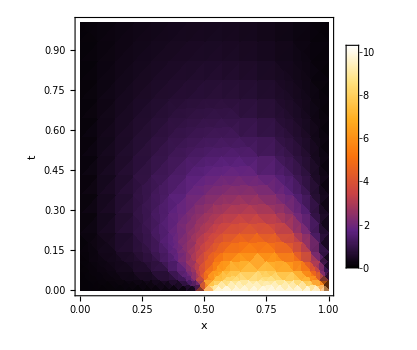

```mathematica
plot = DensityPlot[ T1, {x,0,1},{y,0,1},
ImageSize->350,
FrameLabel->{"x","t"},
ColorFunction->"SunsetColors",
PlotLegends->Automatic,
PlotRangePadding->None,
PlotRange->All,
LabelStyle->{FontFamily->"Times",20,Black}
]
```

## 6.b)

Agora da item anterior tenho: T(x,y)=∑_(n=1)^∞ sen(k_n x)[OverTilde[a_n]ℯ^ky+ OverTilde[b_n]ℯ^-ky] (6.15). Usando a condição T(x,L_y)=0 (6.16), tenho:
→T(x,L_y)=∑_(n=1)^∞ sen(k_n x)[OverTilde[a_n]ℯ^kL_y+ OverTilde[b_n]ℯ^-kL_y] = 0
	↦OverTilde[a_n]ℯ^kL_y+ OverTilde[b_n]ℯ^-kL_y=0 →-OverTilde[a_n]ℯ^(2 kL_y)= OverTilde[b_n]
Com isso, T(x,y)=∑_(n=1)^∞ sen(k_n x)OverTilde[a_n[]ℯ^ky-ℯ^(2 kL_y)ℯ^-ky] = ∑_(n=1)^∞ sen(k_n x)A_n sinh[K_n(y-L_y)] (6.17). Digo que A_n→ A_n/(sinh(k_n L_y)), assim: T(x,y)=∑_(n=1)^∞ sen(k_n x)A_n sinh[K_n(y-L_y)]/(sinh(k_n L_y))(6.18).
Agora calculo então, A_n = 2/L_x∫_0^L_x T(x,0)sin(k_n x)ⅆx = 2/L_x∫_(L_x/2)^L_x T_1 sin(k_n x)ⅆx = (2 T_1)/nπ[cos(nπ/2)-cos(nπ)] (6.19).
Por fim, temos então que: T(x,y)=∑_(n=1)^∞ (2 T_1)/nπ[cos(nπ/2)-cos(nπ)]sen(k_n x)sinh[K_n(y-L_y)]/(sinh(k_n L_y))(6.20)

```mathematica
(*Supondo Subscript[T, 1] = 10,Subscript[L, x]=1 e Subscript[L, y]=1*)
nmaxT2 = 100;
kt2 = n*π;
A2n = (2*10)/(n*π)(Cos[(n *π)/2]-Cos[n *π]) ;
T2 = Sum[A2n* Sin[kt2*x]*Sinh[kt2(y-1)]/Sinh[kt2],{n,1,nmaxT2}];
```

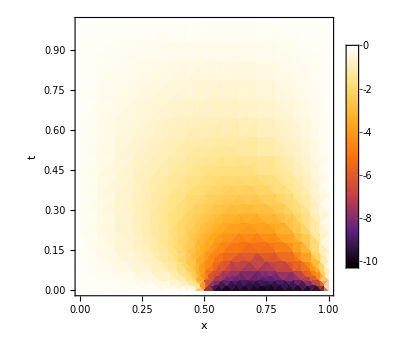

```mathematica
plot = DensityPlot[ T2, {x,0,1},{y,0,1},
ImageSize->350,
FrameLabel->{"x","t"},
ColorFunction->"SunsetColors",
PlotLegends->Automatic,
PlotRangePadding->None,
PlotRange->All,
LabelStyle->{FontFamily->"Times",20,Black}
]
```

## 6.c)

Para esse item usarei as contas deduzidas nas notas de aula, onde para u(x,0) = T'_1 (6.20) e u(x,L_y) = T'_2 (6.21), temos que: u(x,y) = T'_1 +( T'_2- T'_1)/L_y y (6.22). Adaptando para o nosso caso, tenho: T(x,y)=T_2/L_y y (6.23)

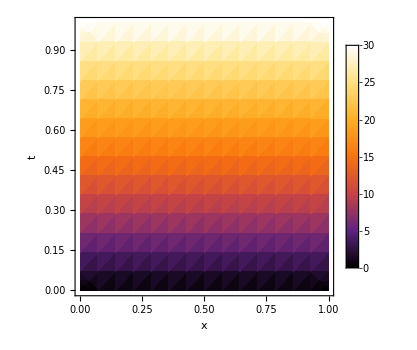

```mathematica
(*Supondo Subscript[L, x]=1, Subscript[L, y]=1 e Subscript[T, 2]= 30*)
plot = DensityPlot[ 30y, {x,0,1},{y,0,1},
ImageSize->350,
FrameLabel->{"x","t"},
ColorFunction->"SunsetColors",
PlotLegends->Automatic,
PlotRangePadding->None,
PlotRange->All,
LabelStyle->{FontFamily->"Times",20,Black}
]
```

## 7.a)

Nessa segunda parte da analise do oscilador harmonico quântico, a solução da equação de Schrodinger ⅈℏ(∂ψ)/(∂t)=Hψ (7.1) terá o seguinte formato ψ(x,t)=∑_n c_n ℯ^(-ⅈE_nt/ℏ)ψ_n(x) (7.2), onde ψ_n(x) e E_n são as soluções da equação ordinária diferencial: Hψ = Eψ (7.3). 
Usando o resultado da questão 3, e sendo:  a^†=√(mω/(2ℏ))(x - ⅈp/mω) (7.4) e   ψ_0(x)=α ℯ^(-mω/(2ℏ)x.b2) (7.5), com α = (mω/ℼℏ)^(1/4)(7.6). Obterei ψ_1=a^†ψ_0(7.7).
→ ψ_1=a^†ψ_0 = √(mω/(2ℏ))(x - ⅈp/mω)α ℯ^(-mω/(2ℏ)x.b2) = α √(mω/(2ℏ))(x  ℯ^(-mω/(2ℏ)x.b2)- ℏ/mω ⅆ/ⅆx ℯ^(-mω/(2ℏ)x.b2)) = α √(mω/(2ℏ))(x  ℯ^(-mω/(2ℏ)x.b2)+x  ℯ^(-mω/(2ℏ)x.b2)) = α √(mω/(2ℏ))2x  ℯ^(-mω/(2ℏ)x.b2)= (mω/ℼℏ)^(1/4)√(mω/(2ℏ))2x  ℯ^(-mω/(2ℏ)x.b2) = 2(mω/ℼℏ)^(3/4)x  ℯ^(-mω/(2ℏ)x.b2)
Portanto, ψ_1=2(mω/ℼℏ)^(3/4)x  ℯ^(-mω/(2ℏ)x.b2) (7.8)

## 7.b)

Agora mostrarei que ψ_1 é uma solução da equação Hψ=Eψ, E_1=3ℏω/2 (7.9). Para isso usarei a hamiltoniana no seguinte formato: H= ℏω(a^†a + 1/2) (7.10).
→Hψ_1= 2(ℏω(mω/(2ℏ)))^(3/4)(a^†a x  ℯ^(-mω/(2ℏ)x.b2) + (x  ℯ^(-mω/(2ℏ)x.b2))/2)
	↦a x  ℯ^(-mω/(2ℏ)x.b2) = √(mω/(2ℏ))(x + ℏ/mω ⅆ/ⅆx) x  ℯ^(-mω/(2ℏ)x.b2) = √(mω/(2ℏ))(x .b2 ℯ^(-mω/(2ℏ)x.b2) + ℏ/mω(1-mω/ℏ x.b2)  ℯ^(-mω/(2ℏ)x.b2) ) = √(mω/(2ℏ)) ℏ/mω  ℯ^(-mω/(2ℏ)x.b2)  = √(ℏ/(2mω)) ℯ^(-mω/(2ℏ)x.b2) 
	↦ a^†a x  ℯ^(-mω/(2ℏ)x.b2)= a^†√(ℏ/(2mω)) ℯ^(-mω/(2ℏ)x.b2) = √(mω/(2ℏ))(x - ⅈp/mω)√(ℏ/(2mω)) ℯ^(-mω/(2ℏ)x.b2)= 1/2(x  ℯ^(-mω/(2ℏ)x.b2)-ℏ/mω ⅆ/ⅆx ℯ^(-mω/(2ℏ)x.b2)) = 1/2(x  ℯ^(-mω/(2ℏ)x.b2)+x ℯ^(-mω/(2ℏ)x.b2)) = x ℯ^(-mω/(2ℏ)x.b2)
→Hψ_1= 2(ℏω(mω/(2ℏ)))^(3/4)(a^†a x  ℯ^(-mω/(2ℏ)x.b2) + (x  ℯ^(-mω/(2ℏ)x.b2))/2) = 2(ℏω(mω/(2ℏ)))^(3/4)(x ℯ^(-mω/(2ℏ)x.b2) + (x  ℯ^(-mω/(2ℏ)x.b2))/2) = 3(ℏω(mω/(2ℏ)))^(3/4)x ℯ^(-mω/(2ℏ)x.b2) 
→Hψ_1= 3(ℏω(mω/(2ℏ)))^(3/4)x ℯ^(-mω/(2ℏ)x.b2)  =  3/2 ℏω  ψ_1 = E_1 ψ_1
Com isso, temos que E_1=3/2 ℏω  (7.11).